Approximation of Landscape of hotspots (V) as a function of ε

## Third order approximation

```mathematica
ClearAll["Global`*"]
```

### Third order approximation of Mimimun activity (Linf) as a function of L

```mathematica
SX = x /.Solve[L(x-x^2/2+x^3/3)==x, x]
```

{0,(3 L-√3 √(16 L-13 L^2))/(4 L),(3 L+√3 √(16 L-13 L^2))/(4 L)}

```mathematica
Linf= FullSimplify[1+SX[[2]]]
```

7/4-(√(48-39 L))/(4 √L)

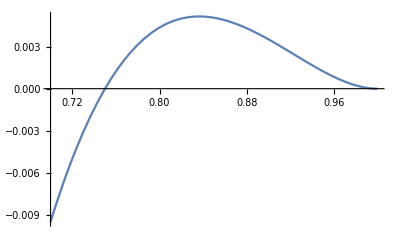

```mathematica
Plot[1- 2 *L +Linf,{L,0.7,1}]
```

### Approximation of mean activity (L) as a function of ε

```mathematica
serie= Series[(1-L) (1-Linf)/ (L^2),{L,1,3}]
```

2 (L-1)^2-10/3 (L-1)^3+O[L-1]^4

```mathematica
SL = L/. Solve[Normal[serie ]== eps,L]
```

{1/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3)),6/5+(1+ⅈ √3)/(5 2^(1/3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))+((1-ⅈ √3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/(10 2^(2/3)),6/5+(1-ⅈ √3)/(5 2^(1/3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))+((1+ⅈ √3) (-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/(10 2^(2/3))}

```mathematica
L= SL[[1]]
```

1/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))

### Landscape of hotspots (V) as a function of ε

#### rho = Ne * v * r_0 * \alpha

```mathematica
V =(1- 2 *L +Linf)/ (4 rho)
```

1/(4 rho)(11/4-2/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))-(√5 √(48-39/5 (6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))))/(4 √(6-2^(2/3)/((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))-((-4+75 eps+5 √3 √(-8 eps+75 eps^2))^(1/3))/2^(2/3))))

```mathematica
FullSimplify[Series[V,{eps,0,2}]]
```

eps/(12 rho)-(11 eps^(3/2))/(18 (√2 rho))+(139 eps^2)/(108 rho)+O[eps]^(5/2)